# Cypher

There will be spoilers here.

```mathematica
Aoff=ToCharacterCode["A"][[1]];
```

## 1 - Steganography

#### 8

science is knowledge is power

```mathematica
data={0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,0,1}
parts=Partition[data,5]
```

{0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,0,1}

{{0,0,0,0,1},{0,0,0,0,0},{0,0,0,1,0},{0,1,1,1,0},{0,1,1,0,1}}

```mathematica
FromDigits[#,2]&/@parts+Aoff//FromCharacterCode
```

BACON

## 2 - Transposition

TH, IN, ER, RE, AN, HE

### 2

TEEESRHDEBNAHHEMRE HJWLAEIDNEETTELTE

```mathematica
data="TEEESRHDEBNAHHEMRE HJWLAEIDNEETTELTE";
```

```mathematica
words=StringSplit[data]
```

{TEEESRHDEBNAHHEMRE,HJWLAEIDNEETTELTE}

```mathematica
Riffle[ToCharacterCode@words[[1]],ToCharacterCode@words[[2]]]//FromCharacterCode
```

THEJEWELSAREHIDDENBENEATHTHEELMTREE

#### bad tree

```mathematica
noEs=StringReplace[data,"E"->""]
```

TSRHDBNAHHMR HJWLAIDNTTLT

```mathematica
Manipulate[Mod[ToCharacterCode[noEs]-Aoff+a,26]+Aoff//FromCharacterCode,{{a,0,"rot"},0,26,1}]
```

### 3

NOITCELFER

```mathematica
StringReverse["NOITCELFER"]
```

REFLECTION

### 4

S N E J D G N
T T E X A R O
N E X X T D A
I X X N H H E
A N R T O I E
S S X O R X D
A S S E U U O

```mathematica
data="SNEJDGNTTEXARONEXXTDAIXXNHHEANRTOIESSXORXDASSEUUO";
```

```mathematica
data2=Partition[Characters@data,7]
```

{{S,N,E,J,D,G,N},{T,T,E,X,A,R,O},{N,E,X,X,T,D,A},{I,X,X,N,H,H,E},{A,N,R,T,O,I,E},{S,S,X,O,R,X,D},{A,S,S,E,U,U,O}}

assassinXenXrouteXtrustXnoXoneXhideXthejadedragon

### 5

QRTSQEKIQDTAQNWA

RTS EKI DTA NWA

```mathematica
rows=Partition[Characters@StringReplace["QRTSQEKIQDTAQNWA","Q"->""],6];
rows//MatrixForm
```

(R | T | S | E | K | I
D | T | A | N | W | A)

```mathematica
StringRiffle@Permutations[Characters@"ETAT"]
```

E T A T
E T T A
E A T T
T E A T
T E T A
T A E T
T A T E
T T E A
T T A E
A E T T
A T E T
A T T E

### 6

TEAUYUOSHNNTRRBTEPAIENROMLMNTTIL

### 7

C T Q I
G K E S
L A N U
  E E N

### 8

TUTT MOWS IHIN OSMR NEPI EEUZ LXSE SZ

## 3 - Monoalphabetic Substitution

```mathematica
subMono[phrase_String,alpha_String]:=StringReplace[phrase,Rule@@@({Characters["ABCDEFGHIJKLMNOPQRSTUVWXYZ"],Characters[alpha]}ᵀ)];
engLetFreq={8.1,1.6,3.2,3.7,12.3,2.3,1.6,5.1,7.2,.1,.5,4.0,2.3,7.2,7.9,2.3,.2,6.0,6.6,9.6,3.1,.9,2.0,.2,1.9,.1}/100;
engLetFreqLbl=Partition[Riffle[Characters["ABCDEFGHIJKLMNOPQRSTUVWXYZ"],engLetFreq],2];
```

#### Tests

```mathematica
subMono["AOEUZ",StringReverse@"ABCDEFGHIJKLMNOPQRSTUVWXYZ"]
```

ZLVFA

```mathematica
Total@engLetFreq
```

1.

### 1

THSWQD THZ RBXP GWXP HG XL ZWRNBRHK UTPQ WQ KBQZBQ,
     g   d so e t  e  t    d s os     e      o do ,
W THZ SWRWGPZ GTP IOWGWRT XMRPMX, HQZ XHZP RPHOFT
    d   s ted t e    t s    se  ,   d   de se
HXBQD GTP IBBVR HQZ XHNR WQ GTP KWIOHOL OPDHOZWQD
  o g t e  oo s   d    s    t e          eg  d  g   
GOHQRLKSHQWH; WG THZ RGOMFV XP GTHG RBXP ABOPVQBUKPZDP
t   s       ;  t   d st      e t  t so    o e  o  edge
BA GTP FBMQGOL FBMKZ THOZDL AHWK GB THSP RBXP
o  t e  o  t    o  d    d        to    e so e
WXNBOGHQFP WQ ZPHKWQD UWGT H QBIKPXHQ BA GTHG FBMQGOL.
   o t   e    de    g   t     o  e    o  t  t  o  t  .

```mathematica
subMono["GOHQRLKSHQWH",".O.G..T........E.S.......D"]
```

T...S.......

```mathematica
subMono["THSWQD THZ RBXP GWXP HG XL ZWRNBRHK UTPQ WQ KBQZBQ,
W THZ SWRWGPZ GTP IOWGWRT XMRPMX, HQZ XHZP RPHOFT
HXBQD GTP IBBVR HQZ XHNR WQ GTP KWIOHOL OPDHOZWQD
GOHQRLKSHQWH; WG THZ RGOMFV XP GTHG RBXP ABOPVQBUKPZDP
BA GTP FBMQGOL FBMKZ THOZDL AHWK GB THSP RBXP
WXNBOGHQFP WQ ZPHKWQD UWGT H QBIKPXHQ BA GTHG FBMQGOL.",".O.G..TAB.....RENSVH..IM.D"]
```

HAVING HAD SOME TIME AT M. DIS.OSA. .HEN IN .ONDON,
I HAD VISITED THE BRITISH M.SE.M, AND MADE SEAR.H
AMONG THE BOO.S AND MA.S IN THE .IBRAR. REGARDING
TRANS..VANIA; IT HAD STR... ME THAT SOME .ORE.NO..EDGE
O. THE .O.NTR. .O..D HARDG. .AI. TO HAVE SOME
IM.ORTAN.E IN DEA.ING .ITH A NOB.EMAN O. THAT .O.NTR..

```mathematica
subMono["GOHQRLKSHQWH",".O.G..TAB.LY..RENSVH..IM.D"]
```

TRANSYLVANIA

### 2

LGGK VHZXJ RP VJJCEVO CK ZMX MGEXO C SCLDGEXJXS
LGRX IVIXJL CK ZMX IGDQXZ GH ZMX SJXLL UMCDM C MVS
ZVQXK HJGR PGBJ OVWGJVZGJP. VZ HCJLZ C MVS
KXNOXDZXS SMXR, WBZ KGU ZMVC C UVL VWOX ZG SXDCIMXJ
ZMX DMVJJVDZXJL CK UMCDM ZMXP UXJX UJCZZXK, C
WXNVK ZG LZBSP ZMAR UCZM SCOCNXKDX.

A  B  C  D  E  F  G  H  I  J  K  L  M  N  O  P  Q  R  S  T  U  V  W  X  Y  Z
00 03 18 09 03 00 14 04 04 16 10 10 18 03 06 05 02 05 09 00 07 16 04 29 00 24

```mathematica
counts={{"A",0},{"B",3},{"C",18},{"D",9},{"E",3},{"F",0},{"G",14},{"H",4},{"I",4},{"J",16},{"K",10},{"L",10},{"M",18},{"N",3},{"O",6},{"P",5},{"Q",2},{"R",5},{"S",9},{"T",0},{"U",7},{"V",16},{"W",4},{"X",29},{"Y",0},{"Z",24}};
```

```mathematica
ordCounts=Sort[counts,#1⟦2⟧>#2⟦2⟧&]
ordFreqs=Sort[engLetFreqLbl,#1⟦2⟧>#2⟦2⟧&]
```

{{X,29},{Z,24},{M,18},{C,18},{V,16},{J,16},{G,14},{L,10},{K,10},{S,9},{D,9},{U,7},{O,6},{R,5},{P,5},{W,4},{I,4},{H,4},{N,3},{E,3},{B,3},{Q,2},{Y,0},{T,0},{F,0},{A,0}}

{{E,0.123},{T,0.096},{A,0.081},{O,0.079},{N,0.072},{I,0.072},{S,0.066},{R,0.06},{H,0.051},{L,0.04},{D,0.037},{C,0.032},{U,0.031},{P,0.023},{M,0.023},{F,0.023},{W,0.02},{Y,0.019},{G,0.016},{B,0.016},{V,0.009},{K,0.005},{X,0.002},{Q,0.002},{Z,0.001},{J,0.001}}

```mathematica
rls={#1⟦1⟧,#2⟦1⟧}&[ordCountsᵀ,ordFreqsᵀ]ᵀ
```

{{X,E},{Z,T},{M,A},{C,O},{V,N},{J,I},{G,S},{L,R},{K,H},{S,L},{D,D},{U,C},{O,U},{R,P},{P,M},{W,F},{I,W},{H,Y},{N,G},{E,B},{B,V},{Q,K},{Y,X},{T,Q},{F,Z},{A,J}}

```mathematica
StringReplace["LGGK VHZXJ RP VJJCEVO CK ZMX MGEXO C SCLDGEXJXS
LGRX IVIXJL CK ZMX IGDQXZ GH ZMX SJXLL UMCDM C MVS
ZVQXK HJGR PGBJ OVWGJVZGJP. VZ HCJLZ C MVS
KXNOXDZXS SMXR, WBZ KGU ZMVC C UVL VWOX ZG SXDCIMXJ
ZMX DMVJJVDZXJL CK UMCDM ZMXP UXJX UJCZZXK, C
WXNVK ZG LZBSP ZMAR UCZM SCOCNXKDX.",Rule@@@rls]
```

RSSH NYTEI PM NIIOBNU OH TAE ASBEU O LORDSBEIEL
RSPE WNWEIR OH TAE WSDKET SY TAE LIERR CAODA O ANL
TNKEH YISP MSVI UNFSINTSIM. NT YOIRT O ANL
HEGUEDTEL LAEP, FVT HSC TANO O CNR NFUE TS LEDOWAEI
TAE DANIINDTEIR OH CAODA TAEM CEIE CIOTTEH, O
FEGNH TS RTVLM TAJP COTA LOUOGEHDE.

```mathematica
rls2={{"X","E"},{"Z","T"},{"M","A"},{"C","I"},{"V","N"},{"J","O"},{"G","S"},{"L","R"},{"K","H"},{"S","L"},{"D","D"},{"U","C"},{"O","U"},{"R","P"},{"P","M"},{"W","F"},{"I","W"},{"H","Y"},{"N","G"},{"E","B"},{"B","V"},{"Q","K"},{"Y","X"},{"T","Q"},{"F","Z"},{"A","J"}};
StringReplace["LGGK VHZXJ RP VJJCEVO CK ZMX MGEXO C SCLDGEXJXS
LGRX IVIXJL CK ZMX IGDQXZ GH ZMX SJXLL UMCDM C MVS
ZVQXK HJGR PGBJ OVWGJVZGJP. VZ HCJLZ C MVS
KXNOXDZXS SMXR, WBZ KGU ZMVC C UVL VWOX ZG SXDCIMXJ
ZMX DMVJJVDZXJL CK UMCDM ZMXP UXJX UJCZZXK, C
WXNVK ZG LZBSP ZMAR UCZM SCOCNXKDX.",Rule@@@rls2]
```

RSSH NYTEO PM NOOIBNU IH TAE ASBEU I LIRDSBEOEL
RSPE WNWEOR IH TAE WSDKET SY TAE LOERR CAIDA I ANL
TNKEH YOSP MSVO UNFSONTSOM. NT YIORT I ANL
HEGUEDTEL LAEP, FVT HSC TANI I CNR NFUE TS LEDIWAEO
TAE DANOONDTEOR IH CAIDA TAEM CEOE COITTEH, I
FEGNH TS RTVLM TAJP CITA LIUIGEHDE.

```mathematica
subMono["LGGK VHZXJ RP VJJCEVO CK ZMX MGEXO C SCLDGEXJXS
LGRX IVIXJL CK ZMX IGDQXZ GH ZMX SJXLL UMCDM C MVS
ZVQXK HJGR PGBJ OVWGJVZGJP. VZ HCJLZ C MVS
KXNOXDZXS SMXR, WBZ KGU ZMVC C UVL VWOX ZG SXDCIMXJ
ZMX DMVJJVDZXJL CK UMCDM ZMXP UXJX UJCZZXK, C
WXNVK ZG LZBSP ZMAR UCZM SCOCNXKDX.","..a.........h........o.E.T"]
```

.... o.TE. .. o..a.o. a. ThE h..E. a .a....E.E.
...E .o.E.. a. ThE ....ET .. ThE ..E.. .ha.h a ho.
To.E. .... .... .o...oT.... oT .a..T a ho.
.E..E.TE. .hE., ..T ... Thoa a .o. o..E T. .E.a.hE.
ThE .ho..o.TE.. a. .ha.h ThE. .E.E ..aTTE., a
.E.o. T. .T... Th.. .aTh .a.a.E..E.

## Polyalphabetic Substitution

### 1

FLASH
ZTVGLKDBGLRUHABTUOZ

```mathematica
data="ZTVGLKDBGLRUHABTUOZ";
```

```mathematica
key=StringRepeat["FLASH",5,StringLength[data]]
```

FLASHFLASHFLASHFLAS

```mathematica
FromCharacterCode[Mod[ToCharacterCode["ABC"]-Aoff+ToCharacterCode["ABC"]-Aoff+1,26]+Aoff]
```

BDF

```mathematica
FromCharacterCode[Mod[ToCharacterCode[#1]-Aoff-ToCharacterCode[#2]-Aoff-1,26]+Aoff]&[Characters[data],Characters[key]]
```

{T,H,U,N,D,E,R,A,N,D,L,I,G,H,T,N,I,N,G}

## Challenge Puzzles

### 1

Periodic Table one

N, S, Cl, Eu, U

7, 16, 17, 63, 92

```mathematica
FromCharacterCode[Aoff+Mod[#,26]&/@{7,16,17,63,92}]
```

HQRLO

### 5

Music one

E, EG, G, A, GBDE, EGCG, EGCE, E, DGC

### 7

Geometry one

```mathematica
z=π .955
```

3.00022

```mathematica
x=Sin[38*π/180]*6.479
```

3.98887

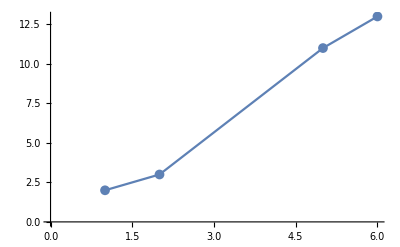

```mathematica
ListLinePlot[{{1,2},{2,3},{5,11},{6,13}},PlotMarkers->{Automatic, 10}]
```

```mathematica
y=18
```

18

```mathematica
FromCharacterCode[Mod[BitShiftRight[#,4],18]+3&/@{50,20,37,95,74,0,25,51,5,78,34,32,72}+Aoff-1]
```

FDEHGCDFCGEEG

### 11

TT-AA-AG-AG-CG-TG
AC-AT-GA-AG-AG-AT

DNA Transcription:
A↔T
G↔C
RNA Transcription:
A→U
T→A
G↔C

```mathematica
StringReplace["TT-AA-AG-AG-CG-TG
AC-AT-GA-AG-AG-AT",{"A"->"T","T"->"A","G"->"C","C"->"G"}]
```

AA-TT-TC-TC-GC-AC
TG-TA-CT-TC-TC-TA

```mathematica
StringReplace["TT-AA-AG-AG-CG-TG
AC-AT-GA-AG-AG-AT",{"A"->"U","T"->"A","G"->"C","C"->"G"}]
```

AA-UU-UC-UC-GC-AC
UG-UA-CU-UC-UC-UA

AAU, UUC, UCG, CAC, UGU, ACU, UCU, CUA

Asn(N), Phe(F), Ser(S), His(H), Cys(C), Thr(T), Ser(S), Leu(L)

TTA, AAG, AGC, GTG, ACA, TGA, AGA, GAT

Leu(L), Lys(K), Ser(S), Val(V), Thr(T), Stp(*), Arg(R), Gly(G)